# Planning a Kibble Balance

Maiyun Zhang^*

*: Pearson College UWC, Victoria, BC V9C 4H7, Canada

## Introduction

A Kibble balance is used to accurately measure gravitational force and therefore define the kilogram. This paper describes the the process of making and operating an amateur-grade Kibble balance.

## Estimations

### Magnetic Force

We are using some copper 32 AWG wire to make the coil.

Diameter:

```mathematica
dWire=Quantity[0.127, "Millimeters"] 92^((36-32)/39)
```

0.201938 mm

Cross-section area:

```mathematica
wireArea = Pi (dWire/2)^2
```

0.0320277 mm^2

Resistivity:

```mathematica
rWire[l_]:=l/wireArea Entity["Element","Copper"][EntityProperty["Element","Resistivity"]]
```

The circuit is powered at  and there is a shunt of  (%) in series with the coil. The magnetic flux density is approximately  according to the manufacturer. When the current is constant, there is no induced voltage across the coil.

:

```mathematica
force[L_]:=Quantity[12100, "Gauss"] Quantity[3.3, "Volts"]/(rWire[L]+ Quantity[500, "Ohms"])L
```

Force at infinity length:

```mathematica
UnitSimplify@Limit[force[Quantity[x, "Meters"]], x->Infinity]
```

7.52274 N

Plot force vs. length of wire:

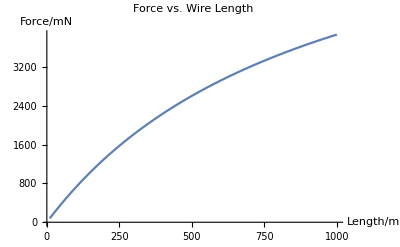

```mathematica
Plot[UnitConvert[force[Quantity[x, "Meters"]], "Millinewtons"],]
```

As one can see, the measurable range increases as the length increases.

Example range at 200m:

```mathematica
UnitSimplify[force[Quantity[200, "Meters"]]/Quantity[9.81, ("Newtons")/("Kilograms")]]
```

0.134299 kg

## Instrument Parameters

To complete a measurement, one needs several parameters: .

### Gravitational Acceleration

Here, we use a pendulum to measure the acceleration due to gravity, .

The period of the pendulum is a function of the length, , angle of oscillation, , and the local acceleration due to gravity, .

```mathematica
PendulumPeriod[θ_, l_, iter_:2, g_:9.81]:=2Pi Sqrt[l/g]Sum[Product[(2m-1)/(2m),{m, 1, n}]^2 Sin[θ/2]^(2n),{n, 0, iter}]
```

```mathematica
PendulumPeriod[50/180 Pi, 1627/1000]
```

2.68455

Similarly,  can be obtained from the periods by fitting the equations.